-Graphics-

FittedModel[17.8027+31476. x]

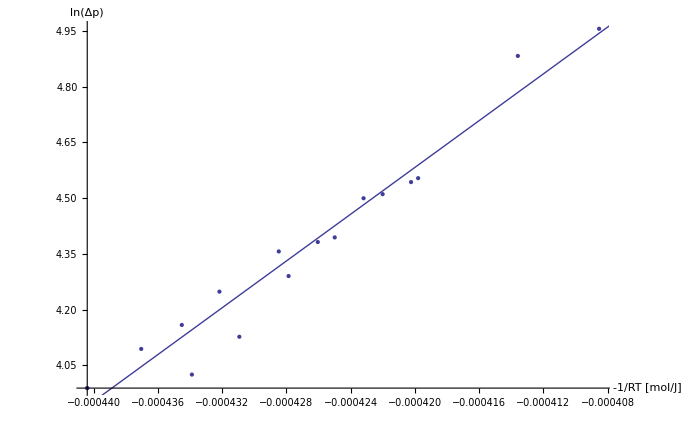

```mathematica
(* Aufgabe 4 *)
diff[h_]:=h-466;
fallend={{21.4,466-324},{17.8,461-329},{13.2, 442-348},{11.2,440-350},{9.3, 435-355},{7.7, 435-357}, {5.3, 431-361},{3.8, 428-364},{2.2, 426-366},{0.1, 423-369}};
steigend={{0.1, 423-369},{4.2, 424-368},{6.1,427-365},{8.1,435-362},{10.0,439-358},{12.0,444-353},{13.5,446-351}};
Rasterize[ListPlot[{fallend, steigend},PlotStyle->{{Red, Thick, PointSize[Large]}, {Blue, Thick, PointSize[Large]}}, AxesLabel->{Temperatur °C, Δp torr},PlotLegends->{fallende Temperatur,steigende Temperatur}], ImageSize->700]

p0:=746.31;
gerade=List[];
xF[liste_,i_]:=-1/(8.3144621*(273+liste[[i]][[1]]));
(*yF[liste_,i_]:=Log[(p0+liste[[i]][[2]] )/p0 ];*)
yF[liste_,i_]:=Log[(liste[[i]][[2]] ) ];

For[i=1,i<=Length[fallend],i++,AppendTo[gerade,{xF[fallend, i],yF[fallend, i]} ]];
For[i=1,i<=Length[steigend],i++,AppendTo[gerade,{xF[steigend, i],yF[steigend, i]} ]];
model=LinearModelFit[gerade,x,x]
Show[ListPlot[gerade],Plot[model["BestFit"],{x,-1,0}],AxesLabel->{"-1/RT [mol/J]", "ln(Δp)"}]
```